```mathematica
ClearAll["Global`*"]
```

Derive the\chi^2 dependence of energy density by inversion

```mathematica
ϵ[χ2]=(χ2+μ^2)*(3*χ2-μ^2)/(2*λ)
```

((μ^2+χ2) (-μ^2+3 χ2))/(2 λ)

```mathematica
Solve[(χ2+μ^2)*(3*χ2-μ^2)/(2*λ)==ϵ,χ2]
```

{{χ2→1/3 (-μ^2-√2 √(3 ϵ λ+2 μ^4))},{χ2→1/3 (-μ^2+√2 √(3 ϵ λ+2 μ^4))}}

```mathematica
f[p_,η_]=Exp[I*p*Cosh[η]]
g[p_,ϕ_]=Exp[-I*p*Cos[ϕ]]
h1[p_,η_]=Cos[p*Cosh[η]]
h2[p_,η_]=Sin[p*Cosh[η]]
```

ⅇ^(ⅈ p Cosh[η])

ⅇ^(-ⅈ p Cos[ϕ])

Cos[p Cosh[η]]

Sin[p Cosh[η]]

```mathematica
Integrate[g[ϕ],{ϕ,0,2*Pi}]
```

∫_0^(2 π) g[ϕ]ⅆϕ

```mathematica
ps=Range[0.01,50,0.1];
```

```mathematica
h1ps=NIntegrate[h1[ps,η],{η,0,10}];
h2ps=NIntegrate[h2[ps,η],{η,0,10}];
```

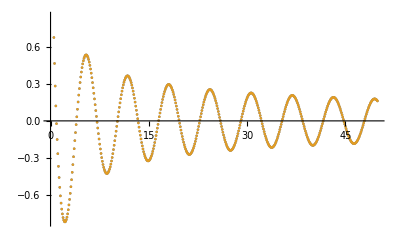

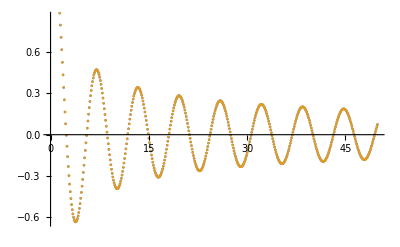

```mathematica
ListPlot[{
Transpose@{ps,h1ps},
Transpose@{ps,-Pi/2*BesselY[0,ps]}
}]
ListPlot[{
Transpose@{ps,h2ps},
Transpose@{ps,Pi/2*BesselJ[0,ps]}
}]
```

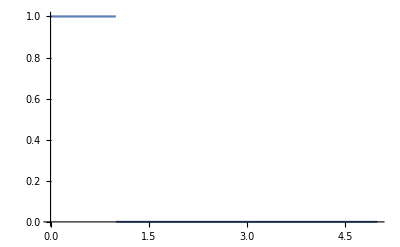

```mathematica
ϕ[r_]=HeavisideTheta[1-r];
Plot[ϕ[r],{r,0,5}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {1.00494}. NIntegrate obtained -0.317965 and 0.000806564 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {1.00494}. NIntegrate obtained -0.322817 and 0.000817644 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {1.00494}. NIntegrate obtained -0.331199 and 0.000835509 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

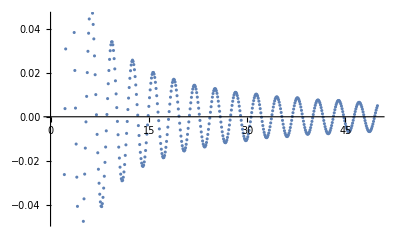

```mathematica
ϕ[r_]=HeavisideTheta[1-r];
ps=Range[0.01,50,0.1];

dr=0.01;
rmin=0.01;
rmax=10;
rs=Range[rmin,rmax,dr];

fNintps=NIntegrate[r*ps*ϕ[r]*BesselJ[0,r*ps]*BesselY[1,ps],{r,rmin,rmax}];
fSum[p_]=dr*Total[rs*p*ϕ[rs]*BesselJ[0,rs*p]*BesselY[1,p]];
fSumps=fSum[ps];

A=ListPlot[{
Transpose@{ps,fNintps},
Transpose@{ps,fSumps}
}]
```

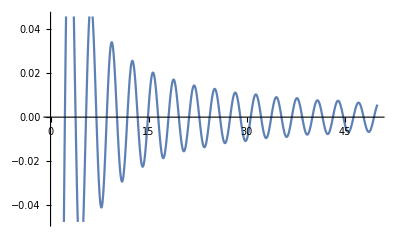

```mathematica
f[p_]=Integrate[r*p*ϕ[r]*BesselJ[0,r*p]*BesselY[1,p],{r,rmin,rmax}];
B=Plot[f[p],{p,0,50}]
```

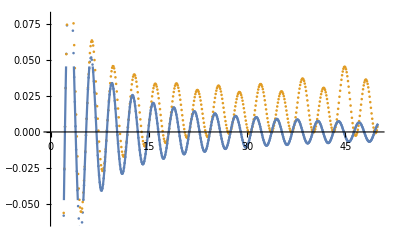

```mathematica
Show[A,B]
```

```mathematica
a={1,2,3,4,5}
b=a^2
```

{1,2,3,4,5}

{1,4,9,16,25}

```mathematica
Transpose[{a,b}]
```

{{1,1},{2,4},{3,9},{4,16},{5,25}}

```mathematica
test=Interpolation[Transpose[{a,b}]]
```

InterpolatingFunction[…]

```mathematica
test[2.5]
```

6.25

```mathematica
x[r_,ϕ_]=r*Cos[ϕ];
y[r_,ϕ_]=r*Sin[ϕ];
z[τ_,η_]=τ*Cosh[η];
t[τ_,η_]=τ*Sinh[η];

r[x_,y_]=Sqrt[x^2+y^2];
τ[t_,z_]=Sqrt[t^2-z^2];
ϕ[x_,y_]=ArcTan[y/x];
η[z_,t_]=ArcTanh[z/t];
```

```mathematica
F=f[τ[t,z],r[x,y]];
(-D[F,{t,2}]+D[F,{x,2}]+D[F,{y,2}]+D[F,{z,2}])/.x->x[r,ϕ]/.y->y[r,ϕ]/.z->z[τ,η]/.t->t[τ,η]//FullSimplify
```

(f^(0,1)[√(-τ^2),√(r^2)])/(√(r^2))+f^(0,2)[√(-τ^2),√(r^2)]-(f^(1,0)[√(-τ^2),√(r^2)])/(√(-τ^2))-f^(2,0)[√(-τ^2),√(r^2)]

```mathematica
ClearAll["Global`*"]
DSolve[-(1/τ)*D[τ*D[y[τ,r],{τ,1}],{τ,1}]==A*y[τ,r],y[τ,r],τ]
```

{{y[τ,r]→BesselJ[0,√A τ] C[1]+BesselY[0,√A τ] C[2]}}

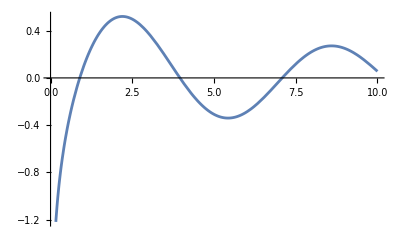

```mathematica
Plot[BesselY[0,x],{x,0,10}]
```

```mathematica
BesselY[0,I]//N
```

-0.268032+1.26607 ⅈ

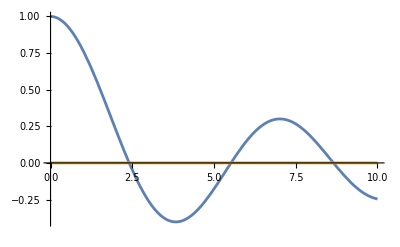

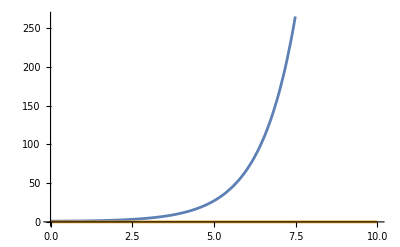

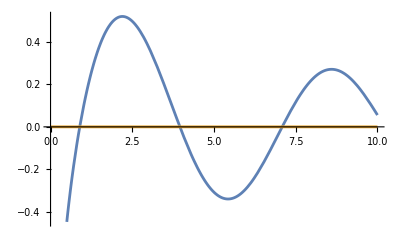

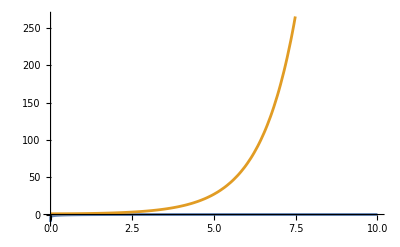

```mathematica
Plot[{Re@BesselJ[0,x],Im@BesselJ[0,x]},{x,0,10}]
Plot[{Re@BesselJ[0,I*x],Im@BesselJ[0,I*x]},{x,0,10}]
Plot[{Re@BesselY[0,x],Im@BesselY[0,x]},{x,0,10}]
Plot[{Re@BesselY[0,I*x],Im@BesselY[0,I*x]},{x,0,10}]
```

```mathematica
Integrate[1/Sqrt[m^2-x^2-y^2],{y,-Sqrt[m^2-x^2],Sqrt[m^2-x^2]}]
```

ConditionalExpression[π, x^2<m^2]

```mathematica
Integrate[Sin[x],{x,0,Pi}]
```

2

```mathematica
Integrate[2*Sqrt[m^2-x^2],{x,-m,m}]
```

m √(m^2) π